# Solving Linear Systems

All our algorithms have internal steps where they to solve linear systems
	A x=b
Our matrices are always symmetric and several of the algorithms need positive definite.

The plan is to try to explain several things about solving linear systems and detecting if a matrix is positive definite.

## Solving generic moderate sized A x=b

A general solver computes an LU decomposition A=LU and then solves the two triangular systems A x=b as L y=b and U x=y.  Most of the work is in the LU decomposition.  The LU decomposition needs n^2 space and 2/3 n^3 flops.  It also needs to pivot rows and/or columns.

For moderate sized generic problems this is the default solver in matlab, mathematica, julia, ...

```mathematica
n=1234;
A=RandomReal[{-1,1},{n,n}]; b=RandomReal[{-1,1},n];
{n,AbsoluteTiming[LinearSolve[A,b];]⟦1⟧}
{n,AbsoluteTiming[LUDecomposition[A]]⟦1⟧}
```

{1234,0.0637008}

{1234,0.0482115}

## Solving SPD A x=b

An SPD solver computes a Cholesky decomposition A=L Lᵀ and then solves the two triangular systems A x=b as L y=b and Lᵀ x=y.  Most of the work is in the Cholesky decomposition.  The decomposition needs 0.5 n^2 space and 1/3 n^3 flops.  It does NOT needs to pivot.  It is usually about half the time of an LU decomposition.

This is the smart (and traditional) thing to do

```mathematica
Data=Table[
A=RandomReal[{-1,1},{n,n}];A=A.Aᵀ+IdentityMatrix[n];
{n,AbsoluteTiming[U=CholeskyDecomposition[A];]⟦1⟧},
{n,{12,45,56,123,1234,3456,6000,10000}}]
```

{{12,0.0330495},{45,0.0000562},{56,0.0000457},{123,0.0001898},{1234,0.0267261},{3456,0.23568},{6000,0.94246},{10000,3.676}}

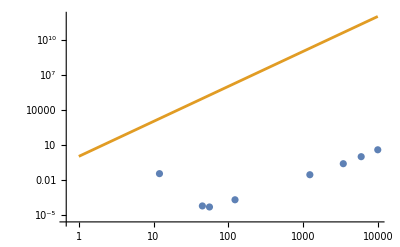

```mathematica
ListLogLogPlot[{Data,
{{1,1^3},{10^4,10^12}}},
Joined->{False,True}]
```

```mathematica
n=723;
A=RandomReal[{-1,1},{n,n}]; b=RandomReal[{-1,1},n];
A=A.Aᵀ;
{{n,AbsoluteTiming[U=CholeskyDecomposition[A];]⟦1⟧},
{n,AbsoluteTiming[LUDecomposition[A]]⟦1⟧}}
L=Uᵀ;
MatrixPlot[L,PlotLabel->Norm[L.Lᵀ-A]]
```

{{723,0.0284999},{723,0.0092187}}

-Graphics-

## Detecting SPD

Efficient storage of a symmetric matrix takes 0.5 n^2 slots. Operations on efficiently store symmetric matrices take about half the time of a general matrix. It is easy to check if a matrix is symmetric.

The smart (and traditional) way to check if a symmetric matrix is SPD is to attempt to compute a Cholesky decomposition.  If it completes the matrix is SPD.  Cholesky decompositions all quit gracefully (with a warning) if a matrix is not SPD.

```mathematica
n=12;
A=RandomReal[{-1,1},{n,n}];
A=A+Aᵀ;
CholeskyDecomposition[A]
```

CholeskyDecomposition::posdef: The matrix {«1»,{-0.132471,-0.417671,-0.515221,0.602865,-«19»,«18»,«19»,-0.374152,-0.545185,-1.09734,«2»},«8»,«2»} is not sufficiently positive definite to complete the Cholesky decomposition to reasonable accuracy.

CholeskyDecomposition[{{-1.11581,-0.132471,-0.178496,-1.2583,-1.3506,0.457446,0.286209,-0.82026,-1.22025,1.30012,0.14804,1.07791},{-0.132471,-0.417671,-0.515221,0.602865,-0.663503,0.772069,1.74037,-0.374152,-0.545185,-1.09734,-0.739583,0.249069},{-0.178496,-0.515221,-1.33356,-0.321321,-0.396165,0.781764,-0.368073,0.622102,1.17497,1.35211,1.14308,0.714631},{-1.2583,0.602865,-0.321321,0.971183,0.860519,0.158801,1.12421,-0.674945,-0.350893,1.51854,-1.25551,0.259263},{-1.3506,-0.663503,-0.396165,0.860519,-0.409692,1.70469,-0.130668,-0.440916,0.58212,-0.569508,-1.05833,0.362166},{0.457446,0.772069,0.781764,0.158801,1.70469,0.467045,0.223664,-1.47148,-1.16685,1.02398,-0.322024,-0.568265},{0.286209,1.74037,-0.368073,1.12421,-0.130668,0.223664,-1.1189,-0.386881,-0.507762,0.860191,0.1496,-0.922302},{-0.82026,-0.374152,0.622102,-0.674945,-0.440916,-1.47148,-0.386881,1.43803,-0.961226,-0.559446,0.692783,0.238223},{-1.22025,-0.545185,1.17497,-0.350893,0.58212,-1.16685,-0.507762,-0.961226,-1.70369,1.4474,0.0653788,-1.18379},{1.30012,-1.09734,1.35211,1.51854,-0.569508,1.02398,0.860191,-0.559446,1.4474,1.55249,-0.0499232,0.479785},{0.14804,-0.739583,1.14308,-1.25551,-1.05833,-0.322024,0.1496,0.692783,0.0653788,-0.0499232,0.885378,-1.10264},{1.07791,0.249069,0.714631,0.259263,0.362166,-0.568265,-0.922302,0.238223,-1.18379,0.479785,-1.10264,1.05959}}]

The warning is triggered when the algorithm attempts to take the square root of a negative number!  See the pseudocode on Wikipedia

https://en.wikipedia.org/wiki/Cholesky_decomposition#:~:text=for%20(i%20%3D%200,%2D%20sum))%3B%0A%20%20%20%20%7D%0A%7D

Bottom level library routines provide mechanisms to “continue” the factorization.  One continuation “stunt” simply flips the sign under the square root. Another “stunt” replaces the negative value with a small positive value.   These continuation “stunts” produce a lower triangular matrix L with a positive definite L Lᵀ looking vaguely like A!

The reason these features persist is that they were traditional in Line Search based Newton optimization algorithms.  This is described on p54.